#### Input parameters

```mathematica
B1=1; H=.7; B2=.1; eA= 2 10^7; roA=1; L1=Sqrt[B1^2 + H^2]; L2= Sqrt[B2^2 + H^2];
r=eA H^3/ ( 3 Sqrt[3] L1^3);Alpha=100;Lam=-1;
```

#### K = Stiffness Matrix ; R = Loading

```mathematica
K=eA/L1^3 {{B1^2 + Alpha L1^3 B2^2 /L2^3, -B1 H},{-B1 H, H^2}};
R=Lam{{0},{-r}};
```

#### M = Mass matrix ; DD = Damping matrix ; U = Displacement ;

```mathematica
MS[Bet_,Alpha1_,Alpha2_]:=Module[{M,DD,U},
M= roA/3 {{L1+Bet L2,0},{0,L1}};DD=Alpha1 M + Alpha2 K;U=LinearSolve[K,R];
{M,DD,U}]
```

#### EiVals = Eigen Values ; EiVecs = Eigen Vectors ; T = Cycle ; w = Frequencies ;

```mathematica
Eigen[Bet_,Alpha1_,Alpha2_]:=Module[{Eigensys,EiVals,EiVecs,T,w},
Eigensys=Eigensystem[{K,MS[Bet,Alpha1,Alpha2][[1]]}];
EiVals={Eigensys[[1,2]],Eigensys[[1,1]]};EiVecs={-Eigensys[[2,2]],Eigensys[[2,1]]};
w=Sqrt[EiVals];T=2 Pi/w;
{EiVals,EiVecs,T,w}]
```

#### Kdiag = K diagonal ; Mdiag = M diagonal ; Th = Eigen Vectors

```mathematica
ModT[Bet_,Alpha1_,Alpha2_]:=Module[{M,DD,Mbar,Kbar,DDbar,Th,Kdiag,Mdiag,Ddiag},
M= MS[Bet,Alpha1,Alpha2][[1]];DD=MS[Bet,Alpha1,Alpha2][[2]];
Th=Transpose[Eigen[Bet,Alpha1,Alpha2][[2]]];Mbar=Transpose[Th] .M.Th;
Kbar=Transpose[Th] .K.Th;DDbar=Transpose[Th] .DD.Th;
Kdiag=Diagonal[Kbar];Mdiag=Diagonal[Mbar];
Ddiag=Diagonal[DDbar];
{Kdiag,Mdiag,Ddiag,Th}]
```

#### Ana : Analytical solutions ; AnaSol = Solutions up to n_timesteps

```mathematica
Ana[Bet_,Alpha1_,Alpha2_,t_,u0_,v0_]:=Module[{w,Si,wD,u0Bar,v0Bar,uBar,vBar,aBar,u,v,a},
w=Eigen[Bet,Alpha1,Alpha2][[4]];
Si=ModT[Bet,Alpha1,Alpha2][[3]]/(2 w ModT[Bet,Alpha1,Alpha2][[2]]);
wD=w Sqrt[1-Si^2];
u0Bar=LinearSolve[ModT[Bet,Alpha1,Alpha2][[4]],u0];
v0Bar=LinearSolve[ModT[Bet,Alpha1,Alpha2][[4]],v0];

uBar=Exp[-Si w t] (u0Bar Cos[wD t] + (v0Bar + Si w u0Bar)/(wD) Sin[wD t]);
vBar=1/wD ⅇ^(-Si t w) (v0Bar wD Cos[t wD]-(Si v0Bar w+Si^2 u0Bar w^2+u0Bar wD^2) Sin[t wD]);
aBar=1/wD ⅇ^(-Si t w) (-wD (2 Si v0Bar w+Si^2 u0Bar w^2+u0Bar wD^2) Cos[t wD]+(Si^2 v0Bar w^2+Si^3 u0Bar w^3-v0Bar wD^2+Si u0Bar w wD^2) Sin[t wD]);

u=ModT[Bet,Alpha1,Alpha2][[4]].uBar;
v=ModT[Bet,Alpha1,Alpha2][[4]].vBar;
a=ModT[Bet,Alpha1,Alpha2][[4]].aBar;
{u,v,a}]
AnaSol[Bet_,Alpha1_,Alpha2_,t_,dt_,u0_,v0_]:=Module[{nt,tt,u1,u2,v1,v2,a1,a2},
nt=t/dt;tt=dt Range[nt];
u1=Table[0,nt];u2=Table[0,nt];
v1=Table[0,nt];v2=Table[0,nt];
a1=Table[0,nt];a2=Table[0,nt];
For[i=1,i<=nt,i++,
u1[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[1,1]];
u2[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[1,2]];
v1[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[2,1]];
v2[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[2,2]];
a1[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[3,1]];
a2[[i]]=Ana[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[3,2]];
];
{u1,u2,v1,v2,a1,a2}
]
```

## 4. Time integration - Newmark method

#### TimeInt : Time Integral Solver

```mathematica
TimeInt[Bet_,Alpha1_,Alpha2_,t_,dt_,u0_,v0_,P_,Am_,Af_,Ga_,Bet1_]:=Module[{M,DD,r,nt,u,v,a,Keff,reff,u1,u2,v1,v2,a1,a2},
M=MS[Bet,Alpha1,Alpha2][[1]];DD=MS[Bet,Alpha1,Alpha2][[2]];
r={0,0};
nt=t/dt;
u[0]=u0;v[0]=v0;
a[0]=-Inverse[M] .(DD . v[0] + K.u[0]);
Keff=(1-Am)/(Bet1 dt^2)M+(Ga(1-Af))/(Bet1 dt)DD+(1-Af) K;
For[i=0,i<=nt,i++,
reff=r-Af K.u[i]+DD.((Ga(1-Af))/(Bet1 dt)u[i]+(Ga-Ga Af-Bet1)/Bet1 v[i]+((Ga-2 Bet1) (1-Af) dt)/(2 Bet1)a[i])+M.((1-Am)/(Bet1 dt^2)u[i]+(1-Am)/(Bet1 dt)v[i]+(1-Am-2 Bet1)/(2 Bet1)a[i]);
u[i+1] = LinearSolve[Keff,reff];
v[i+1]=Ga/(Bet1 dt)(u[i+1]-u[i])-(Ga-Bet1)/Bet1 v[i]-(Ga-2 Bet1)/(2 Bet1)dt a[i];
a[i+1]=1/(Bet1 dt^2)(u[i+1]-u[i])-1/(Bet1 dt)v[i]-(1-2 Bet1)/(2 Bet1)a[i];
];

u1=Table[u[i][[1]],{i,0,nt}];u2=Table[u[i][[2]],{i,0,nt}];
v1=Table[v[i][[1]],{i,0,nt}];v2=Table[v[i][[2]],{i,0,nt}];
a1=Table[a[i][[1]],{i,0,nt}];a2=Table[a[i][[2]],{i,0,nt}];

{u1,u2,v1,v2,a1,a2}
]
```

#### NewMarkFamily : NewMark Schemes ~ Classic , Hilber , Bossak , NewMark-Alpha

```mathematica
NewMarkFamily[type_,Bet_,Alpha1_,Alpha2_,t_,dt_,u0_,v0_,p_]:=Module[{Am,Af,Ga,Bet1,Solver,u1,u2,v1,v2,a1,a2},
Switch[type,
(* Method type : NM = NewMark Classic, HI = Hilber , BO = Bossak , NMA = Newmark-Alpha *)

NM,
{Am=0;Af=0;Bet1=1/(p+1)^2;Ga=(3-p)/(2 p +2);
},
HI,
{Am=0;Af=(1-p)/(p+1);Bet1=1/4 (1+Af)^2;Ga=1/2 + Af;},
BO,
{Am=(p-1)/(p+1);Af=0;Bet1=1/4 (1-Am)^2;Ga=1/2 - Am;},
NMA,
{Am=(2p-1)/(p+1); Af=p/(p+1);Ga=1/2 - Am + Af;Bet1=1/4(1 - Am + Af)^2;}
];
Solver=TimeInt[Bet,Alpha1,Alpha2,t,dt,u0,v0,p,Am,Af,Ga,Bet1];
u1=Solver[[1]];u2=Solver[[2]];
v1=Solver[[3]];v2=Solver[[4]];
a1=Solver[[5]];a2=Solver[[6]];
{u1,u2,v1,v2,a1,a2}
]
```

#### NewMark Family vs Analytical Comparison

```mathematica
Comparison[type_,Bet_,Alpha1_,Alpha2_,t_,dt_,u0_,v0_,p_]:=Module[{T1,T2,g1,g2,p1,u1Ana,u1NM,u2Ana,u2NM,v1Ana,v1NM,v2Ana,v2NM,ph1,ph2,ph3,ph4,phase1,phase2},
T1=Eigen[Bet,Alpha1,Alpha2][[3,1]];
T2=Eigen[Bet,Alpha1,Alpha2][[3,2]];
u1Ana=AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[1]];
u2Ana=AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[2]];v1Ana=AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[3]];v2Ana=AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[4]];
u1NM=NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[1]];
u2NM=NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[2]];
v1NM=NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[3]];
v2NM=NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[4]];
g1=ListLinePlot[{Flatten[u1Ana]/B2,Flatten[u1NM]/B2},PlotRange->All,AxesLabel->{"t","u_1/B2"}];
g2=ListLinePlot[{Flatten[u2Ana]/H,Flatten[u2NM]/H},PlotRange->All,AxesLabel->{"t","u_2/H"}];
ph1=Table[0,2,Length[u1Ana]];ph2=Table[0,2,Length[u1Ana]];
ph1[[1]]=Flatten[u1Ana/B2];ph1[[2]]=Flatten[v1Ana  T1/B2];
ph2[[1]]=Flatten[u1NM/B2];ph2[[2]]=Flatten[v1NM  T1/B2];
phase1=ListLinePlot[{Transpose[ph1],Transpose[ph2]},Frame->True,FrameLabel->{"u_1/B2","((u̇)_1)/B2"},PlotRange->{{-.25,.25},{-3.,3.}}];
ph3=Table[0,2,Length[u1Ana]];ph4=Table[0,2,Length[u1Ana]];
ph3[[1]]=Flatten[u2Ana/H];ph3[[2]]=Flatten[v2Ana  T2/H];
ph4[[1]]=Flatten[u2NM/H];ph4[[2]]=Flatten[v2NM  T2/H];
phase2=ListLinePlot[{Transpose[ph3],Transpose[ph4]},Frame->True,FrameLabel->{"u_2/H","((u̇)_2)/H"},PlotRange->{{-.25,.25},{-3.,3.}}];

{Table[{{g1,g2},{phase1,phase2}},1]//TableForm}

]
```

```mathematica
Bet=100;Alpha1=0;Alpha2=0;t=0.02;dt=10^-4;p=1;
u0=MS[Bet,Alpha1,Alpha2][[3]];v0={{0},{0}};
```

#### NewMark Classic vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=0.1ms , p=1

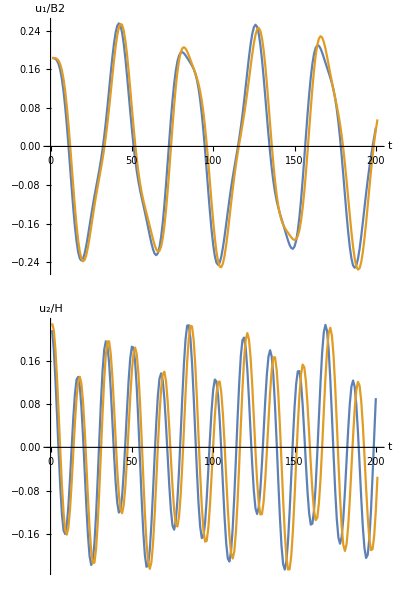
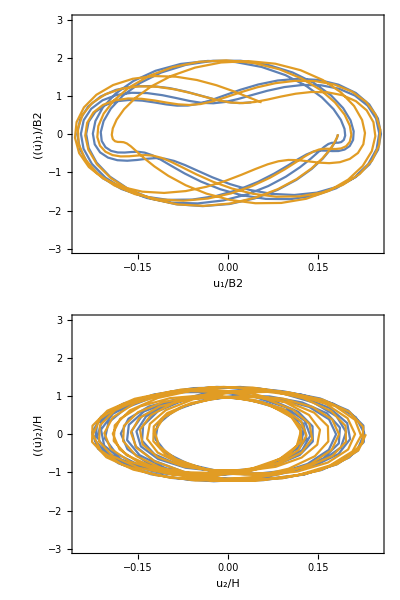
{-Graphics- | -Graphics-}

```mathematica
Comparison[NM,Bet,Alpha1,Alpha2,t,0.1 10^-3,u0,v0,1]
```

#### NewMark Classic vs Analytical Solutions , Bet = 100 , Alpha1 = 0 , Alpha2 = 0 , dt = 0.5 ms , p = 1

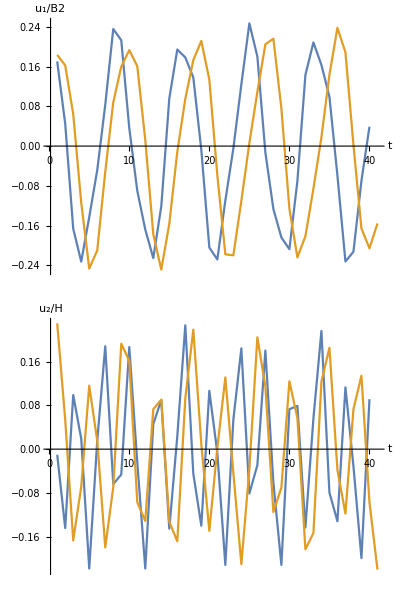
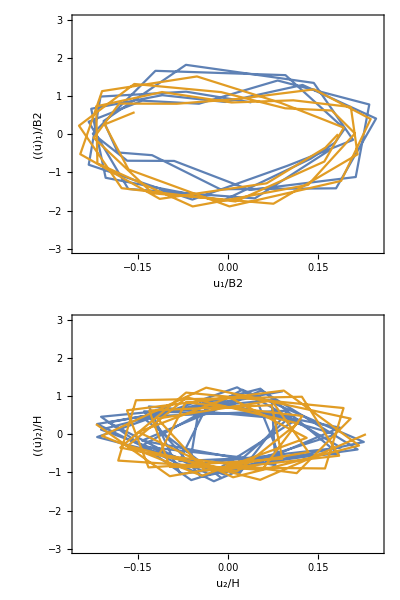
{-Graphics- | -Graphics-}

```mathematica
Comparison[NM,Bet,Alpha1,Alpha2,t,0.5 10^-3,u0,v0,1]
```

#### NewMark Classic vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=1ms , p=1

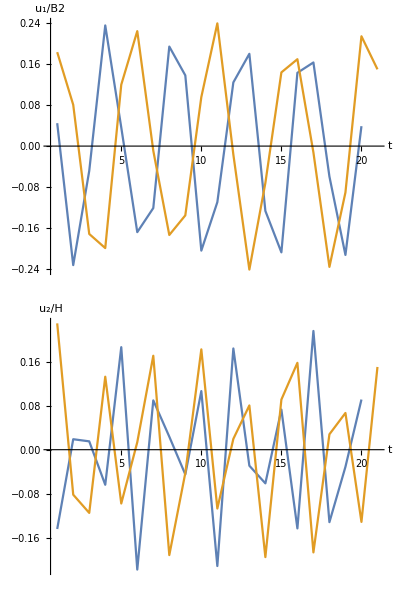
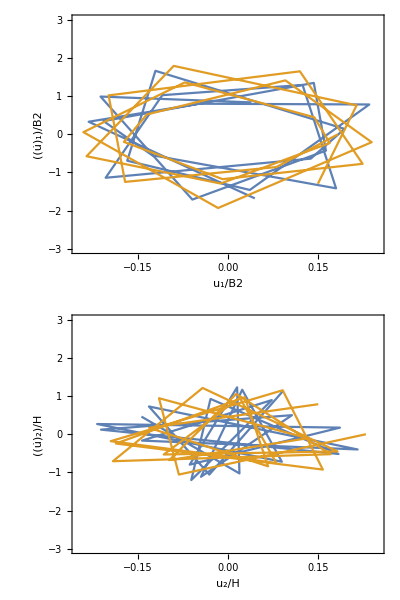
{-Graphics- | -Graphics-}

```mathematica
Comparison[NM,Bet,Alpha1,Alpha2,t,1 10^-3,u0,v0,1]
```

#### Hilber vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=0.1ms , p=1

```mathematica
Comparison[HI,Bet,Alpha1,Alpha2,t,0.1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### Hilber vs Analytical Solutions , Bet = 100 , Alpha1 = 0 , Alpha2 = 0 , dt = 0.5 ms , p = 1

```mathematica
Comparison[HI,Bet,Alpha1,Alpha2,t,0.5 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### Hilber vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=1ms , p=1

```mathematica
Comparison[HI,Bet,Alpha1,Alpha2,t,1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### BOSSAK vs Analytical Solutions , Bet = 100 , Alpha1 = 0 , Alpha2 = 0 , dt = 0.1 ms , p = 1

```mathematica
Comparison[BO,Bet,Alpha1,Alpha2,t,0.1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### BOSSAK vs Analytical Solutions , Bet = 100 , Alpha1 = 0 , Alpha2 = 0 , dt = 0.5 ms , p = 1

```mathematica
Comparison[BO,Bet,Alpha1,Alpha2,t,0.5 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### BOSSAK vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=1ms , p=1

```mathematica
Comparison[BO,Bet,Alpha1,Alpha2,t,1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### NEWMARK ALPHA vs Analytical Solutions , Bet = 100 , Alpha1 = 0 , Alpha2 = 0 , dt = 0.1 ms , p = 1

```mathematica
Comparison[NMA,Bet,Alpha1,Alpha2,t,0.1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### NEWMARK ALPHA vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=0.5ms , p=1

```mathematica
Comparison[NMA,Bet,Alpha1,Alpha2,t,0.5 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### NEWMARK ALPHA vs Analytical Solutions , Bet=100 , Alpha1=0 , Alpha2=0 , dt=1ms , p=1

```mathematica
Comparison[NMA,Bet,Alpha1,Alpha2,t,1 10^-3,u0,v0,1]
```

{-Graphics- | -Graphics-}

#### DisplacementDT : u_(ana(n+1))^Δt

```mathematica
DisplacementDT[Bet_,Alpha1_,Alpha2_,t_,u0_,v0_]:=Module[{w,Si,wD,u0Bar,v0Bar,uBar,u},
w=Eigen[Bet,Alpha1,Alpha2][[4]];
Si=ModT[Bet,Alpha1,Alpha2][[3]]/(2 w ModT[Bet,Alpha1,Alpha2][[2]]);
wD=w Sqrt[1-Si^2];
u0Bar=LinearSolve[ModT[Bet,Alpha1,Alpha2][[4]],u0];
v0Bar=LinearSolve[ModT[Bet,Alpha1,Alpha2][[4]],v0];
uBar=Exp[-Si w t] (u0Bar Cos[wD t] + (v0Bar + Si w u0Bar)/(wD) Sin[wD t]);
u=ModT[Bet,Alpha1,Alpha2][[4]].uBar;
{u}
]
```

```mathematica
ErrorAnalysis[type_,Bet_,Alpha1_,Alpha2_,t_,dt_,u0_,v0_,p_]:=Module[{nt,tt,u,udt,unm,error1,error2,error3,error4},
nt=t/dt;tt=dt Range[nt];
u={AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[1]],AnaSol[Bet,Alpha1,Alpha2,t,dt,u0,v0][[2]]};
unm={NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[1]],NewMarkFamily[type,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[2]]};
udt=Table[DisplacementDT[Bet,Alpha1,Alpha2,tt[[i]],u0,v0][[1]],{i,1,nt}];
error1=Table[0,nt+1];
error2=Table[0,nt];
error3=Table[0,nt];
error4=Table[0,nt];
For[i=1,i<=nt,i++,

For[i=1,i+1<=nt,i++,
(* Local errors *)
error1⟦i+1⟧=Norm[udt[[i+1]]-unm⟦All,i+1⟧]/Norm[unm⟦All,1⟧]; (*(‖Subscript[u, ana(n+1)]^Δt-Subscript[u, n+1]‖)/(‖Subscript[u, 0]‖)*)

error2⟦i+1⟧=Norm[udt[[i+1]]-unm⟦All,i+1⟧]/Norm[unm⟦All,i+1⟧-unm⟦All,i⟧];(*(‖Subscript[u, ana(n+1)]^Δt-Subscript[u, n+1]‖)/(‖Subscript[u, n+1]-Subscript[u, n]‖)*)

(* Global errors *)
error3⟦i+1⟧=Norm[u[[All,i+1]]-unm⟦All,i+1⟧]/Norm[unm⟦All,1⟧];(*(‖Subscript[u, ana(n+1)]-Subscript[u, n+1]‖)/(‖Subscript[u, 0]‖)*)

error4⟦i+1⟧=Norm[u[[All,i+1]]-unm⟦All,i+1⟧]/Norm[unm⟦All,i+1⟧-unm⟦All,i⟧];(*(‖Subscript[u, ana(n+1)]-Subscript[u, n+1]‖)/(‖Subscript[u, n+1]-Subscript[u, n]‖) *)

];
];
{error1,error2,error3,error4}
]
```

```mathematica
Bet=100;Alpha1=0;Alpha2=0;t=20 10^-3;nt=t/dt;tt=dt Range[nt];dt=0.1 10^-3;p=1;
u0=MS[Bet,Alpha1,Alpha2][[3]];v0={{0},{0}};
```

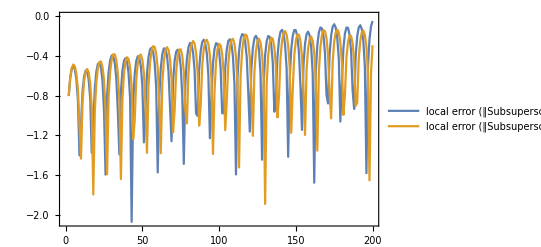
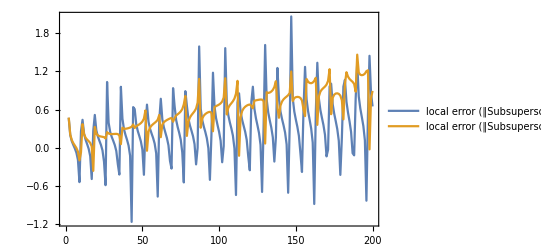
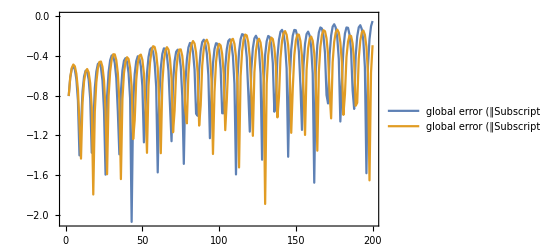
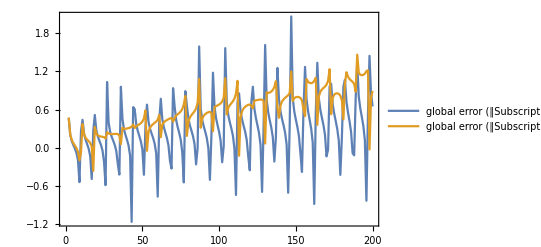
-Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
p1=ListLinePlot[{Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[1]]],Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,0.8][[1]]]},PlotRange->Full,Frame->True,PlotLegends->{"local error (‖SubsuperscriptBox[u, ana (n + 1), Δt] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, 0]‖) - p=1","local error (‖SubsuperscriptBox[u, ana (n + 1), Δt] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, 0]‖) - p=0.8"}];
p2=ListLinePlot[{Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[2]]],Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,.8][[2]]]},PlotRange->Full,Frame->True,PlotLegends->{"local error (‖SubsuperscriptBox[u, ana (n + 1), Δt] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, n + 1] - SubscriptBox[u, n]‖) - p=1","local error (‖SubsuperscriptBox[u, ana (n + 1), Δt] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, n + 1] - SubscriptBox[u, n]‖) - p=0.8"}];
p3=ListLinePlot[{Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[3]]],Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,0.8][[3]]]},PlotRange->Full,Frame->True,PlotLegends->{"global error (‖SubscriptBox[u, ana (n + 1)] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, 0]‖) - p=1","global error (‖SubscriptBox[u, ana (n + 1)] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, 0]‖) - p=0.8"}];
p4=ListLinePlot[{Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,p][[4]]],Log10[ErrorAnalysis[NM,Bet,Alpha1,Alpha2,t,dt,u0,v0,0.8][[4]]]},PlotRange->Full,Frame->True,PlotLegends->{"global error (‖SubscriptBox[u, ana (n + 1)] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, n + 1] - SubscriptBox[u, n]‖) - p=1","global error (‖SubscriptBox[u, ana (n + 1)] - SubscriptBox[u, n + 1]‖)/(‖SubscriptBox[u, n + 1] - SubscriptBox[u, n]‖) - p=0.8"}];
Table[{{p1,p2},{p3,p4}},1]//TableForm
```